```mathematica
ClearAll["Global`*"]
```

```mathematica
B1[n_,m_]:=A/(Sqrt[((4*m^2/(n^2))-1)] )
```

```mathematica
??B1
```

```mathematica
tg[b1_,n_]:= (n*π)/b1
tgnew[b1_,n_]:= n/(b1*Sqrt[2])
```

```mathematica
B1list = N[Table[{tgnew[B1[n,m],n],B1[n,m],n,m},{n,1,30,2},{m,1,20}]/.A->3.03]; (*3.03 for 15N, 2.16 for 145N*)
```

```mathematica
B1listflat = Flatten[B1list,1];
```

```mathematica
B1listnew=Select[B1listflat,Abs[Im[#[[1]]]]<10^-6&];
```

```mathematica
B1listnewsorted=Sort[B1listnew,Abs[#1[[1]]]<Abs[#2[[1]]]&];
```

```mathematica
(*maybe the better idea is to plot the minimal values for each value for n*)
```

```mathematica
mytable = Table[{tgnew[B1[n,m],n],B1[n,m], n , m},{n,1,60,2},{m,1,20}]/.A->2.16;
mytable = Flatten[mytable,1];
mytable =Select[mytable,Im[#[[1]]]<10^-6&];
mytable=Sort[mytable,Abs[#1[[1]]]<Abs[#2[[1]]]&];
mytable=Take[mytable,50]
Export["pointsN14.dat",mytable,"Table"]
```

{{0.567012,1.24708,1,1},{0.866124,2.44921,3,2},{1.08574,3.25632,5,3},{1.26788,3.90397,7,4},{1.26788,0.55771,1,2},{1.42695,4.45984,9,5},{1.56998,4.9543,11,6},{1.70103,5.404,13,7},{1.70103,1.24708,3,3},{1.82269,5.81921,15,8},{1.93671,6.20681,17,9},{1.93671,0.365107,1,3},{2.04439,6.57166,19,10},{2.04439,1.72938,5,4},{2.14667,6.91734,21,11},{2.2443,7.24657,23,12},{2.33785,7.56151,25,13},{2.33785,2.11722,7,5},{2.4278,7.86387,27,14},{2.4278,0.873763,3,4},{2.51453,8.15503,29,15},{2.59837,8.43617,31,16},{2.59837,2.44921,9,6},{2.59837,0.272134,1,4},{2.67959,8.70824,33,17},{2.75842,8.97207,35,18},{2.83506,9.22837,37,19},{2.83506,2.74357,11,7},{2.83506,1.24708,5,5},{2.90968,9.47774,39,20},{3.05345,3.01049,13,8},{3.12286,0.679289,3,5},{3.19075,1.55128,7,6},{3.25723,3.25632,15,9},{3.25723,0.217088,1,5},{3.449,3.48531,17,10},{3.51059,1.81279,9,7},{3.57112,0.990034,5,6},{3.63065,3.70045,19,11},{3.80363,3.90397,21,12},{3.80363,2.04494,11,8},{3.80363,0.55771,3,6},{3.91471,0.180628,1,6},{3.96908,4.09754,23,13},{3.96908,1.24708,7,7},{4.07565,2.25544,13,9},{4.12791,4.28248,25,14},{4.28084,4.45984,27,15},{4.28084,0.825897,5,7},{4.33062,2.44921,15,10}}

pointsN14.dat

```mathematica
"file8new.dat"
```

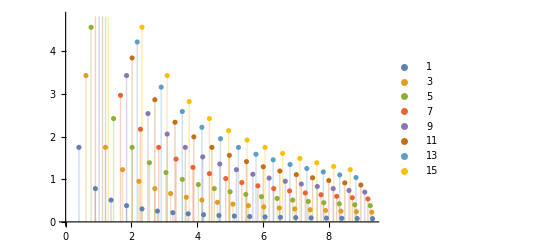

```mathematica
ListPlot[Table[{tgnew[B1[n,m],n],B1[n,m]},{n,1,15,2},{m,1,20}]/.A->3.03,Filling->Axis, PlotLegends->{1,3,5,7,9,11,13,15,17,19,21}]
```

```mathematica
mytable=Table[{tgnew[B1[n,m],n],B1[n,m]},{n,1,7,2},{m,1,10}]/.A->3.03;
```

```mathematica
Export["file7.dat",mytable,"Table"]
```

file7.dat